## definitions

After a renormalization step, a given site i of the n^th approximant becomes either molecular (in which case n becomes n-2) or atomic (n becomes n-3). 
We can thus associate to each site a unique “renormalization path”: the sequence of molecular/atomic sites that has led to it, starting from the trivial (F_n=1) chain and inflating it.

```mathematica
(* take a renormalization path (seq), a site label (i) and an approximant size (n) and return the new renormalization path, the new site label and the new size after one renormalization group operation *)
ClearAll[i,n];
iterSeq[{seq_,i_,n_}]:=Block[{inew=i,seqn=seq,nnew=n},
If[i>Fibonacci[n-1],seqn="m"<>seq;inew=i-Fibonacci[n-1];nnew=n-2;,
If[i>Fibonacci[n-2],seqn="a"<>seq;inew=i-Fibonacci[n-2];nnew=n-3,
seqn="m"<>seq;nnew=n-2;]];
{seqn,inew,nnew}
]
```

In the limit ρ->0 fractal dimensions no longer depend on the site i, but only on the relative time spent on molecular sites, which we shall call x.
Letting n_m be the number of molecular renormalizations and n_a be the number of atomic renormalization, we have
x = n_m/(n_m+n_a)∈ [0, 1/2]

```mathematica
(* false when n<3 *)
test=#[[3]]≥3&;
(* take a site (i), a size (n) and return the renormalization path for this site *)
path[i_,n_]:=NestWhile[iterSeq,{"",i,n},test][[1]]->i
(* compute the relative time spent on molecular sites (x) *)
xPath[i_,n_]:={i,StringCount[NestWhile[iterSeq,{"",i,n},test][[1]],"m"]/n}
```

```mathematica
(* generate the whole (x) tree! *)
tree[n_]:=xPath[#,n]&/@ Range[Fibonacci[n]]
```

```mathematica
(* association map; not necesarily needed: use Position to find positions corresponding to a given x!! *)
hashtree[n_]:=<|Table[i->StringCount[NestWhile[iterSeq,{"",i,n},test][[1]],"m"]/n,{i,1,Fibonacci[n]}]|>
```

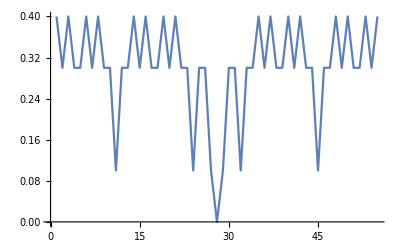

```mathematica
(* wow, such tree, much xs! *)
ListPlot[tree[10],Joined->True]
```

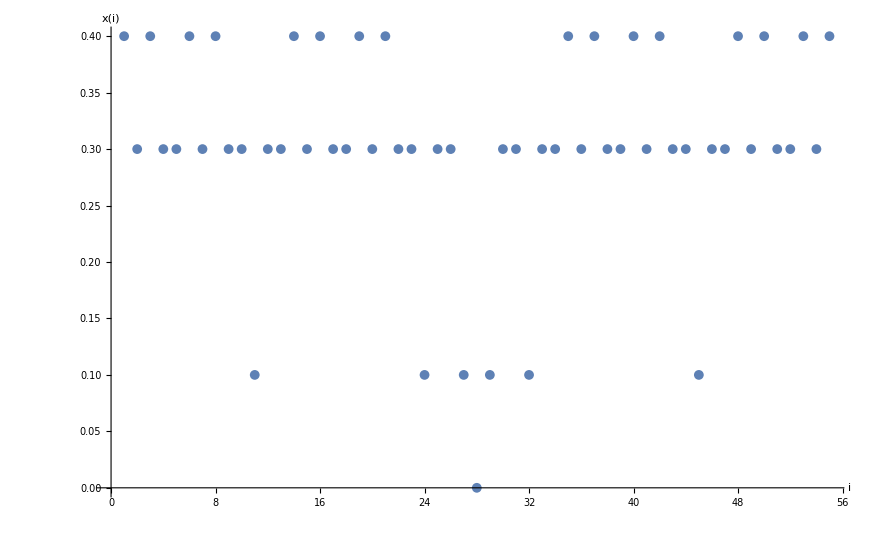

```mathematica
l=tree[10];
m=Max[l];
ListPlot[l,PlotRange->All,PlotStyle->PointSize[.008],Joined->True,ColorFunction->Function[{x,y},ColorData["ThermometerColors"][y ]],AxesLabel->{"i","x(i)"}]/.Line->Point
(*Export[dir<>"data/local_dim_wf_rho_20.png",%,ImageResolution->200]*)
```

```mathematica
Position[tree[10],4/10];
Transpose[%]//First
```

{1,3,6,8,14,16,19,21,35,37,40,42,48,50,53,55}

## Application

### Energy/co-label representation

```mathematica
n=10;

(* compute x for each site *)
xlist=tree[n];
(* drop the site labels, they are unecessary as x is indexed by increasing x label *)
xlist=Last@(Transpose[xlist]);
(* list all possible values of x *)
xvalues=Sort@DeleteDuplicates[xlist];
(* list all positions by increasing value of x *)
listPos=Flatten[Position[xlist,#]]&/@xvalues;

(* intensities by increasing value of x *)
intx=Range[Length[xvalues]];
(* intensity table *)
int=Table[0,{it,Fibonacci[n]}];
MapThread[(int[[#1]]=#2)&,{listPos,intx}];

mask=Table[int[[i]]int[[j]],{i,Fibonacci[n]},{j,Fibonacci[n]}];
```

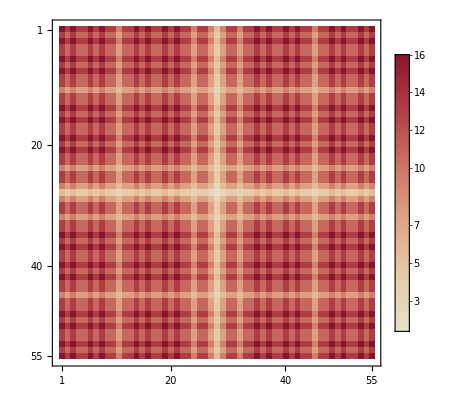

```mathematica
MatrixPlot[mask,ColorFunction->"ThermometerColors",PlotLegends->Automatic]
```

### Labelling energy states

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
n=8;
(* permutation rule reordering sites by increasing x label *)
perm=Ordering@Transpose[tree[n+2]][[2]];

(* wavefunctions in the co-basis, ordered by increasing x label *)
wf=Block[{val,vec,i=n,ts=10.,tw=1.},
{val,vec}=Eigensystem[hp[i,tw,ts]];
(*order wavefunctions by increasing energy*)
vec=vec[[Ordering@val]];
vec=vec[[perm]];
Transpose[Transpose[vec][[perm]]]
];
```

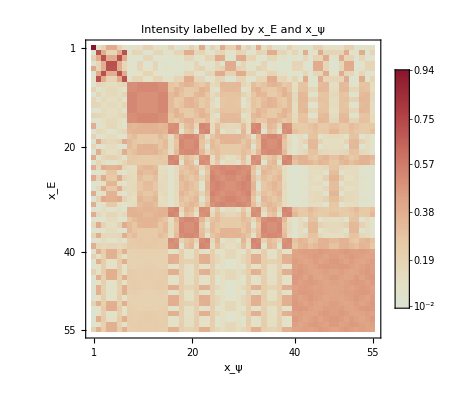

```mathematica
MatrixPlot [Abs[wf]^2,FrameLabel->{"x_E","x_ψ"},PlotLabel->"Intensity labelled by x_E and x_ψ",PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```